```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
p[T_,μB_,μS_,μQ_]:=t[T]x[T,μB,μS,μQ]//Evaluate;
s[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T]];
ρB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB]];
ρQ[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μQ]];
ρS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μS]];
e[T_,μB_,μS_,μQ_]:=T s[T,μB,μS,μQ]+μB ρB[T,μB,μS,μQ]+μQ ρQ[T,μB,μS,μQ]+μS ρS[T,μB,μS,μQ]-p[T,μB,μS,μQ];
χTT[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T,T]];
χTμB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T,μB]];
χTμQ[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T,μQ]];
χTμS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T,μS]];
χμBμB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB,μB]];
χμBμQ[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB,μQ]];
χμBμS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB,μS]];
χμQμQ[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μQ,μQ]];
χμQμS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μS,μQ]];
χμSμS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μS,μS]];
p[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
s[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
ρB[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
ρQ[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
ρS[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
(*e[T,μB,μS,μQ]//FullSimplify*)
χTT[T,μB,μS,μQ]//FullSimplify//TraditionalForm
χTμB[T,μB,μS,μQ]//FullSimplify//TraditionalForm
χTμQ[T,μB,μS,μQ]//FullSimplify//TraditionalForm
χTμS[T,μB,μS,μQ]//FullSimplify//TraditionalForm
χμBμB[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
χμBμQ[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
χμBμS[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
χμQμQ[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
χμQμS[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
χμSμS[T,μB,μS,μQ]//FullSimplify//TraditionalForm;
```

t''(T) x(T,μB,μS,μQ)+2 t'(T) x^(1,0,0,0)(T,μB,μS,μQ)+t(T) x^(2,0,0,0)(T,μB,μS,μQ)

t'(T) x^(0,1,0,0)(T,μB,μS,μQ)+t(T) x^(1,1,0,0)(T,μB,μS,μQ)

t'(T) x^(0,0,0,1)(T,μB,μS,μQ)+t(T) x^(1,0,0,1)(T,μB,μS,μQ)

t'(T) x^(0,0,1,0)(T,μB,μS,μQ)+t(T) x^(1,0,1,0)(T,μB,μS,μQ)

```mathematica
D[1/2(1+Tanh[(T-Tc)/Ts]),T]
D[1/2(1+Tanh[(T-Tc)/Ts]),{T,2}]//FullSimplify
```

Sech[(T-Tc)/Ts]^2/(2 Ts)

-(Sech[(T-Tc)/Ts]^2 Tanh[(T-Tc)/Ts])/Ts^2

```mathematica
data=ReadList["C:\\Users\\chris\\Desktop\\Iccing_conditions_wBSQ_GS5.dat",Real];
data=ArrayReshape[data,{Length[data]/6,6}];
```

```mathematica
ListPlot3D[data[[;;,1;;3]],PlotRange->All]
```

-Graphics3D-

```mathematica
4 3.9554 x^3/(197.3^3 y^4)/.{x->9.597399022,y->1.3758}
```

0.000508287

```mathematica
241 19^3
155 37^3
```

1653019

7851215

```mathematica
10/7 1/4
```

5/14

```mathematica
k[r_,h_]:=Piecewise[{{10/(7π h^2)(1-3/2(Norm[r]/h)^2+3/4(Norm[r]/h)^3),0<Norm[r]<=h},{5/(14π h^2)(2-Norm[r]/h)^3,h<Norm[r]<=2h}},0];
NIntegrate[k[{x,y},3/10],{x,-1,1},{y,-1,1}]
Plot3D[k[{x,y},3/10],{x,-1,1},{y,-1,1},PlotRange->All,Exclusions->None,PlotPoints->50]
```

1.

-Graphics3D-

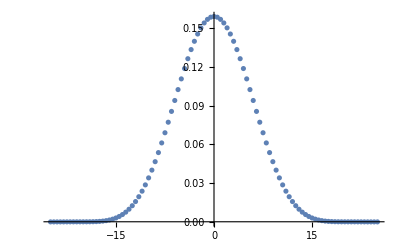

```mathematica
fk[kx_?NumericQ,ky_?NumericQ,h_?NumericQ]:=1/(2π)NIntegrate[E^(I(kx x+ky y))k[{x,y},h],{x,-∞,∞},{y,-∞,∞}]//Chop;
ListPlot[{#,fk[#,0,3/10]}&/@Range[-25,25,1/2]]
```

```mathematica
Integrate[Exp[I a Cos[ϕ]],{ϕ,-π,π},Assumptions->a>0]
```

2 π BesselJ[0,a]

```mathematica
Integrate[r^2 BesselJ[0,kr r],{r,1,2},Assumptions->b>a>0&&kr>0]//FullSimplify
```

1/3 (8 HypergeometricPFQ[{3/2},{1,5/2},-kr^2]-HypergeometricPFQ[{3/2},{1,5/2},-(kr^2/4)])

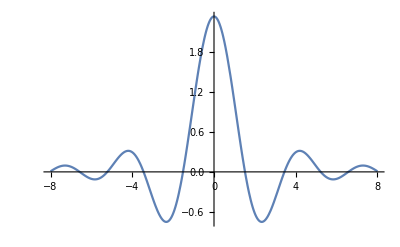

```mathematica
Plot[(1/3) (8 HypergeometricPFQ[{3/2},{1,5/2},-kr^2]-HypergeometricPFQ[{3/2},{1,5/2},-(kr^2/4)]),{kr,-8,8},PlotRange->All]
```